```mathematica
<<Local`QFTToolKit`
<<PhysicalConstants`
<<Units`
```

```mathematica
DeclareIndexFlavor[{dotted,Orange}]
DeclareIndexFlavor[{undotted,Blue}]
DefineTensorShortcuts[{{η,v,D,F,Λ,H,R,τ,μ},1},
{{m},2},
{{σ,ξ},3}
]
AddBaseIndex[{dotted,{1,2}}]
AddBaseIndex[{undotted,{1,2}}]
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}}}

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}},{undotted,{1,2}}}

Lecture 2010.10.01

```mathematica
file=StringReplace[SaveFile,{"10.01"->"09.29"}]
Get[file]
tmpM
tmpV2
subT
tmpS
```

/Users/Tom/Mathematica/StandardModelBeyond/Lecture2010.09.29.out

M_Z^2→(2 ((μ_1^1)^2-Tan[β]^2 (μ_2^2)^2))/(-1+Tan[β]^2)

V→1/8 ((g^2+gp^2) (v1^2-v2^2)^2+8 v1^2 (μ_1^1)^2+8 v2^2 (μ_2^2)^2-8 v1 v2 (μ_3^3)^2)

Tan[β]→v2/v1

Sin[2 β]→((μ_3^3)^2)/((μ_1^1)^2+(μ_2^2)^2)

```mathematica
PR1["The Higgs search has not found m_h<M_Z.  Examine constrains on m_h within the MSSM model given the parameterizations of ",
Subscript[V, MSSM,Higgs]->{{μd[1],μd[2],μd[3]}->{Subscript[M, Z]^2,Tan[β],Subscript[m, A]^2}},

NL,
tmpV=V->(μ^2).(SuperDagger[hd[u]].hd[u]+SuperDagger[hd[d]].hd[d])+g^2/2(SuperDagger[hd[u]].τu[a].hd[u]+SuperDagger[hd[d]].τu[a].hd[d])^2+gp^2/2(SuperDagger[hd[u]].(1/2).hd[u]+SuperDagger[hd[d]].(-1/2).hd[d])^2+SoftOp[(Subscript[m, hu]^2).SuperDagger[hd[u]].hd[u]+(Subscript[m, hd]^2).SuperDagger[hd[d]].hd[d]]-Rephase[((Subscript[m, 3]^2).SuperDagger[hd[u]].(-I τu[2]).hd[d]+SuperDagger[((Subscript[m, 3]^2).SuperDagger[hd[u]].(-I τu[2]).hd[d])])],
NL,
CG["The notation in this expression needs some additions for consistency.  We have added a {I τ}-factor to the Rephase argument to make it complete."],
"We can rephase ",hd[u].hd[d]," such that ",Subscript[m, 3]^2∈ℝ,
NL,"As in the SM for VEV we assign a VEV structure for this case ",
subh={hd[u]->{{0},{v2}},hd[d]->{{v1},{0}}},
NL,"Plugging these into V",Yield,,
tmp=tmpV/.subDaggerCT//simpleDot3[{μ,Subscript[m, 3],Subscript[m, 3]^2}]//ConjugateCTSimplify1[{Subscript[m, 3],Subscript[m, 3]^2,v1,v2},{Subscript[m, _]^2}],Yield,
tmpV1=tmp/.subh//ConjugateCTSimplify1[{Subscript[m, 3],v1,v2},{Subscript[m, _]^2}],Yield,
"Sum over τu[a]->σu[a]/2,{a,1,3}",Yield,
"POFF",
tmp=ExtractPositionPattern[tmpV1,Dot[a___,(τu[_]|ConjugateTranspose[τu[_]]),b___]]/.τu[a_]->σu[a]/2,Yield,
tmp=Map[If[FreeQ[#[[2]],σu[a]],# [[1]]->#[[2]]/.sPauli,
# [[1]]->Sum[#[[2]]/.sPauli,{a,{1,2,3}}]]&,tmp]
,Yield,
"PON",
tmp=ReplacePart[tmpV1,tmp]//.List[a_]:>First[Flatten[a]],
NL,"Substitute: ",sub={Subscript[m, hu]^2->Subscript[m, 1]^2-μ^2,Subscript[m, hd]^2->Subscript[m, 2]^2-μ^2},Yield,
"POFF",
tmp=tmp/.sub//Simplify,Yield,
"PON",
tmp=tmp/.Rephase[a_]->a/.SoftOp[a_]->a//Simplify,Yield,
subn={Subscript[v, 2]->v2,v->v1,Subscript[m, a_]->Subscript[μ, a]},Yield,
tmpV2=tmp=tmp/.subn//FullSimplify,
NL,CG["The above relation for V is similar to the one shown in class except that it differ by factor[2] in the { μ_3^2 v1 v2} term.  Could this be a redefinition of μ_3?"]
];
```

The Higgs search has not found m_h<M_Z.  Examine constrains on m_h within the MSSM model given the parameterizations of V_(MSSM,Higgs)→{{μ_1^1,μ_2^2,μ_3^3}→{M_Z^2,Tan[β],m_A^2}}
V→μ^2.((h_d^d)^†.h_d^d+(h_u^u)^†.h_u^u)+1/2 gp^2 ((h_d^d)^†.(-1/2).h_d^d+(h_u^u)^†.1/2.h_u^u)^2+1/2 g^2 ((h_d^d)^†.τ_a^a.h_d^d+(h_u^u)^†.τ_a^a.h_u^u)^2-Rephase[m_3^2.(h_u^u)^†.(-ⅈ τ_2^2).h_d^d+(m_3^2.(h_u^u)^†.(-ⅈ τ_2^2).h_d^d)^†]+SoftOp[m_hd^2.(h_d^d)^†.h_d^d+m_hu^2.(h_u^u)^†.h_u^u]
The notation in this expression needs some additions for consistency.  We have added a {I τ}-factor to the Rephase argument to make it complete.We can rephase h_u^u.h_d^d such that m_3^2∈ℝ
As in the SM for VEV we assign a VEV structure for this case {h_u^u→{{0},{v2}},h_d^d→{{v1},{0}}}
Plugging these into V
→ NullV→μ^2 (h_d^d)^†.h_d^d+1/8 gp^2 ((h_d^d)^†.h_d^d)^2+μ^2 (h_u^u)^†.h_u^u-1/4 gp^2 (h_d^d)^†.h_d^d (h_u^u)^†.h_u^u+1/8 gp^2 ((h_u^u)^†.h_u^u)^2+1/2 g^2 ((h_d^d)^†.τ_a^a.h_d^d)^2+g^2 (h_d^d)^†.τ_a^a.h_d^d (h_u^u)^†.τ_a^a.h_u^u+1/2 g^2 ((h_u^u)^†.τ_a^a.h_u^u)^2-Rephase[ⅈ (h_d^d)^†.(τ_2^2)^†.h_u^u.m_3^2-ⅈ (h_u^u)^†.τ_2^2.h_d^d m_3^2]+SoftOp[(h_d^d)^†.h_d^d m_hd^2+(h_u^u)^†.h_u^u m_hu^2]
→ V→{{(gp^2 v1^4)/8-1/4 gp^2 v1^2 v2^2+(gp^2 v2^4)/8+v1^2 μ^2+v2^2 μ^2+1/2 g^2 ({{0,v2}}.τ_a^a.{{0},{v2}})^2+g^2 {{0,v2}}.τ_a^a.{{0},{v2}} {{v1,0}}.τ_a^a.{{v1},{0}}+1/2 g^2 ({{v1,0}}.τ_a^a.{{v1},{0}})^2-Rephase[-ⅈ {{0,v2}}.τ_2^2.{{v1},{0}} m_3^2+ⅈ {{v1,0}}.(τ_2^2)^†.{{0},{v2}} m_3^2]+SoftOp[{{v1^2 m_hd^2+v2^2 m_hu^2}}]}}
→ Sum over τu[a]->σu[a]/2,{a,1,3}
→ V→(g^2 v1^4)/8+(gp^2 v1^4)/8-1/4 g^2 v1^2 v2^2-1/4 gp^2 v1^2 v2^2+(g^2 v2^4)/8+(gp^2 v2^4)/8+v1^2 μ^2+v2^2 μ^2-Rephase[v1 v2 m_3^2]+SoftOp[v1^2 m_hd^2+v2^2 m_hu^2]
Substitute: {m_hu^2→-μ^2+m_1^2,m_hd^2→-μ^2+m_2^2}
→ V→1/8 (g^2 v1^4+gp^2 v1^4-2 g^2 v1^2 v2^2-2 gp^2 v1^2 v2^2+g^2 v2^4+gp^2 v2^4+8 v2^2 m_1^2+8 v1^2 m_2^2-8 v1 v2 m_3^2)
→ {v_2→v2,v→v1,m_a_→μ_a}
→ V→1/8 ((g^2+gp^2) (v1^2-v2^2)^2+8 v2^2 μ_1^2+8 v1^2 μ_2^2-8 v1 v2 μ_3^2)
The above relation for V is similar to the one shown in class except that it differ by factor[2] in the { μ_3^2 v1 v2} term.  Could this be a redefinition of μ_3?

```mathematica
PR1["Examine minimum of V[v1,v2] ",
CG["?down to weak scale."],
"{First derivative[wrt[v1,v2]]==0}",
tmp={(D[tmpV2[[2]],{v1,1}]==0),(D[tmpV2[[2]],{v2,1}]==0)},Yield,
tmp=tmp/.g^2+gp^2->g1^2;
tmp=Eliminate[tmp,g1]//Simplify,
NL,"Defining ",subT=Tan[β]->v2/v1," we can get relationship for μ's",
NL,
tmp=tmp/.RuleX[subT,v2]//FullSimplify;
tmp=Map[#/v1&,tmp],Yield,
tmp=Map[# /Sec[β]^2&,tmp]//FullSimplify,Yield,
tmpS=Solve[tmp,Sin[2 β]][[1,1]]
]
```

Examine minimum of V[v1,v2] ?down to weak scale.{First derivative[wrt[v1,v2]]==0}{1/8 (4 (g^2+gp^2) v1 (v1^2-v2^2)+16 v1 μ_2^2-8 v2 μ_3^2)==0,1/8 (-4 (g^2+gp^2) v2 (v1^2-v2^2)+16 v2 μ_1^2-8 v1 μ_3^2)==0}
→ (v1^2+v2^2) μ_3^2==2 v1 v2 (μ_1^2+μ_2^2)
Defining Tan[β]→v2/v1 we can get relationship for μ's
Sec[β]^2 μ_3^2==2 (μ_1^2+μ_2^2) Tan[β]
→ Sin[2 β] (μ_1^2+μ_2^2)==μ_3^2
→ Sin[2 β]→μ_3^2/(μ_1^2+μ_2^2)

```mathematica
PR1["Recall from Standard Model the relations ",
tmpx=tmp=μd[1]^2 v1^2-μd[2]^2 v2^2+(g^2+gp^2)/4(v1^2-v2^2)(v1^2+v2^2)==0,back,
CG["Look up where this comes from!"],and,
NL,subM={Subscript[M, W]->g^2 v^2/2,Subscript[M, Z]^2->(g^2+gp^2)/2(v1^2+v2^2)},
NL,"",
tmp={tmp,
tmp1=Apply[Equal,subM[[2]]]}/.g^2+gp^2->g1^2;
tmp=Eliminate[tmp,g1];
tmp=Solve4Pattern[tmp,Subscript[M, Z]^2][[1,1]],yield,
tmp={tmp,subT}/.Rule->Equal;
tmp=Eliminate[tmp,{v1,v2}];
tmp=Solve4Pattern[tmp,Subscript[M, Z]^2][[1,1]]
]
```

Recall from Standard Model the relations 1/4 (g^2+gp^2) (v1^2-v2^2) (v1^2+v2^2)+v1^2 (μ_1^1)^2-v2^2 (μ_2^2)^2==0 ⟵Look up where this comes from! and 
{M_W→(g^2 v^2)/2,M_Z^2→1/2 (g^2+gp^2) (v1^2+v2^2)}
M_Z^2→-(2 (v1^2 (μ_1^1)^2-v2^2 (μ_2^2)^2))/(v1^2-v2^2) ⟶ M_Z^2→(2 ((μ_1^1)^2-Tan[β]^2 (μ_2^2)^2))/(-1+Tan[β]^2)

```mathematica
PR1[CG["The 2 higgs doublets imply 4 parameters {μ_1,μ_2,μ_3==m_h,v1,v2}(?) but these equations constrain only 3 of them.  The parameters {μ_1,μ_2,μ_3} are determined with constraints from measurements of {M_Z, m_h, Tan[β]}.  ?How is Tan[β] measured?  "]
]
```

The 2 higgs doublets imply 4 parameters {μ_1,μ_2,μ_3==m_h,v1,v2}(?) but these equations constrain only 3 of them.  The parameters {μ_1,μ_2,μ_3} are determined with constraints from measurements of {M_Z, m_h, Tan[β]}.  ?How is Tan[β] measured?

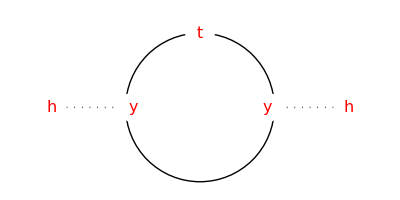
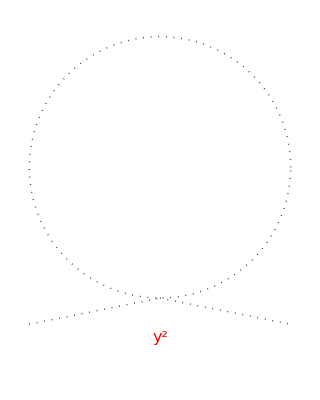
Renormalization Group (RG) scaling of soft operators like (m_ij^ij)^2.(A_i^i)^†.A_j^j
ξ_ijk^ijk.A_i^i.A_j^j.A_k^k+(ξ_ijk^ijk.A_i^i.A_j^j.A_k^k)^†
B_ij^ij.A_i^i.A_j^j
m̃.λ.λThese terms contribute to the radiative corrections.  E.g., the diagrams for R_i^i with the potential coupling W→y.(φ^†.φ)^2 and y.φ.ψ^†.ψ
-Graphics-  +  -Graphics-for loop momentum E>>>m  yields respective expressions -y^2 ∫_{k_i^i} [(k_i^i)^-2]  +  y^2 ∫_{k_i^i} [1/(m^2+(k_i^i)^2)]In the expansion of the integrand for E>>>m quadratic terms cancel but we are left with an integral like ∫_{k_i^i} [(k_i^i)^-4] which generates a logrithmic divergent expression for the mass correction. δ_m^2∼m^2 y^2 ∫_{k_i^i} [(k_i^i)^-4] which we can treat as before by including expressions for Z^-1 and finding expressions for running coupling constants.

```mathematica
scale=1;
MidArrow[xy_]:={Arrow[{xy[[1]],(xy[[1]]+xy[[2]])/2}],Line[{(xy[[1]]+xy[[2]])/2,xy[[2]]}]};
TextOver[text_,xy_]:={White,Disk[xy,0.2scale],
Text[Style[text,FontSize->16,Red],xy]};
Graphics121[h_,t_,x_]:=Graphics[{Thick,Black,
Circle[{0,0},scale],
Dotted,Line[{{-2,0},{-1,0}}],
Line[{{2,0},{1,0}}],
TextOver[x,{.9,-.0}],TextOver[x,{-.9,-.0 }],
TextOver[h,{2,0 }],TextOver[h,{-2,0 }],
TextOver[t,{0,1 }]
}
];
Graphics20[x_]:=Graphics[{Thick,Black,Dotted,
Circle[{0,0},scale],
Line[{{-scale,-1.2 scale},{ 0,-scale}}],
Line[{{0,-scale},{ scale,-1.2 scale}}],
TextOver[x,{0,-1.3 scale}]
}
];
PR1["Renormalization Group (RG) scaling of soft operators like ",
Column[
{(mdd[i,j]^2).SuperDagger[Ad[i]].Ad[j],
ξddd[i,j,k].Ad[i].Ad[j].Ad[k]+SuperDagger[(ξddd[i,j,k].Ad[i].Ad[j].Ad[k])],
Bdd[i,j].Ad[i].Ad[j],
m̃.λ.λ
},Frame->All
],
"These terms contribute to the radiative corrections.  E.g., the diagrams for ",Rd[i],
" with the potential coupling ",
W->y.(SuperDagger[φ].φ)^2,and, y.φ.SuperDagger[ψ].ψ,
NL,Graphics121[h,t,y],"  +  ",Graphics20[y^2],
"for loop momentum E>>>m  yields respective expressions ",
-y^2 IntegralOp[{{kd[i]}},1/kd[i]^2],
"  +  ",
y^2 IntegralOp[{{kd[i]}},1/(kd[i]^2+m^2)],
"In the expansion of the integrand for E>>>m quadratic terms cancel but we are left with an integral like ",
IntegralOp[{{kd[i]}},1/kd[i]^4],
" which generates a logrithmic divergent expression for the mass correction. ",
Subscript[δ, m]^2∼ m^2 y^2 IntegralOp[{{kd[i]}},1/kd[i]^4],
" which we can treat as before by including expressions for Z^-1 and finding expressions for running coupling constants. "
];
```

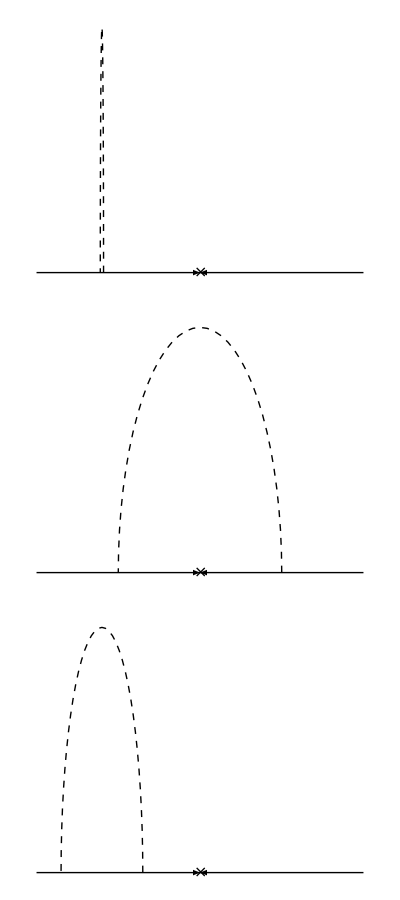
For example, let's look at running gaugino mass term.  We have the diagrams: -Graphics-By dimensional analysis we guess the β-function to have form UnderBar[∂]_{t}[m̃]→(b g^2 m̃)/(16 π) and UnderBar[∂]_{t}[Log[m̃]]→UnderBar[∂]_{t}[Log[g]] which is similar to the standard renormalization group result.

```mathematica
PR1["For example, let's look at running gaugino mass term.  We have the diagrams: ",
Column[
{
Graphics[{Black,Arrowheads[Medium],
Arrow[{{-1,0},{0,0}}],Arrow[{{1,0},{0,0}}],
Text[Style["×",FontSize->16],{0,0}],
Dashed,Circle[{-.6,0},.01,{0,Pi}]},
ImageSize->Small
],
Graphics[{Black,Arrowheads[Medium],
Arrow[{{-1,0},{0,0}}],Arrow[{{1,0},{0,0}}],
Text[Style["×",FontSize->16],{0,0}],
Dashed,Circle[{0,0},.5,{0,Pi}]
},ImageSize->Small
],
Graphics[{Black,Arrowheads[Medium],
Arrow[{{-1,0},{0,0}}],Arrow[{{1,0},{0,0}}],
Text[Style["×",FontSize->16],{0,0}],
Dashed,Circle[{-.6,0},.25,{0,Pi}]
},ImageSize->Small
]
},Frame->All
],
"By dimensional analysis we guess the β-function to have form ",
xPartialD[m̃,{t}]->b/(16π)m̃ g^2,and,
xPartialD[Log[m̃],{t}]->xPartialD[Log[g],{t}],
" which is similar to the standard renormalization group result."
];
```

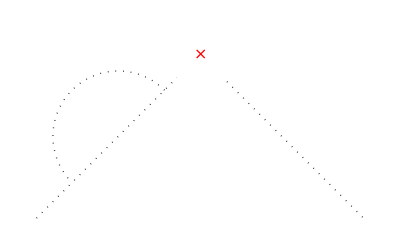
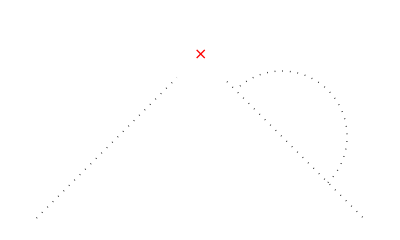
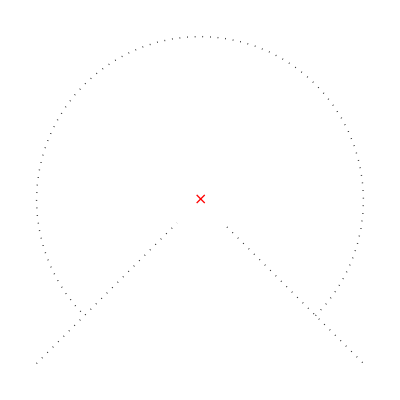
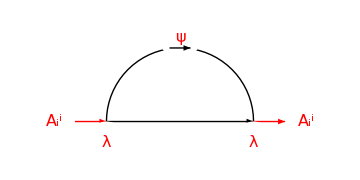
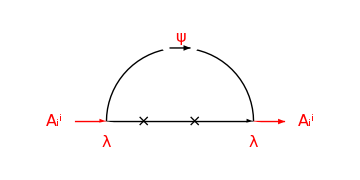
Renormalization group equations for scalar masses.  We have the renormalization group radiative correction diagrams for W→y.φ.φ.φ and λ.A_i^i.ψ.ψ
-Graphics-  +  -Graphics-  +  -Graphics-  =0
but where UnderBar[∂]_{t}[m̃]⊅(b g^2 m̃)/(16 π) the RG expression from the scalar-fermion diagram: -Graphics-Above diagrams has no fermion self-energy terms.  The diagram below has 2 extra sources and breaks SUSY and contributes to gaugino mass correction.  The quadratic divergences exist but cancel.-Graphics-

```mathematica
PR1["Renormalization group equations for scalar masses.  We have the renormalization group radiative correction diagrams for ",
W->y.φ.φ.φ,and,λ.Ad[i].ψ.ψ,
NL,
Graphics[{Thick,Black,Dotted,
Circle[{-.5,-.5},.4,{.25π,1.25 π}],
Line[{{-1,-1 },{ 0,0}}],
Line[{{0,0},{ 1,-1 }}],
TextOver["×",{0,0 }]
}
],"  +  ",
Graphics[{Thick,Black,Dotted,
Circle[{.5,-.5},.4,{-.25π,.75 π}],
Line[{{-1,-1 },{ 0,0}}],
Line[{{0,0},{ 1,-1 }}],
TextOver["×",{0,0 }]
}
],"  +  ",
Graphics[{Thick,Black,Dotted,
Circle[{0,0},1,{-.25π,1.25 π}],
Line[{{-1,-1 },{ 0,0}}],
Line[{{0,0},{ 1,-1 }}],
TextOver["×",{0,0 }]
}
],"  =0
but where ",xPartialD[m̃,{t}]⊅b/(16π)m̃ g^2,
" the RG expression from the scalar-fermion diagram: " ,
radius=.7;
Graphics[{Black,Thick,
Circle[{0,0},radius,{0, π}],
{Red,Thin,
Arrowheads[{.01,.01,.05,.01}],Arrow[{{-1,0},{-radius,0}}],
Arrowheads[{.01,.01,.01,.05}],Arrow[{{radius,0},{1,0}}]
},
Arrowheads[{.01,.05,.01,.01,.01,.05}],Arrow[{{-radius,0},{radius,0}}],
TextOver[Ad[i],{-1.2,0 }],
TextOver[Ad[i],{1.2,0 }],
TextOver[λ,{-radius,-.2 }],TextOver[λ,{radius,-.2 }],
TextOver[ψ,{0,radius+.1 }],
Arrowheads[{.01,.05}],Arrow[{{-.1,radius},{.1,radius}}]
},ImageSize->Medium
],
CG["Above diagrams has no fermion self-energy terms.  The diagram below has 2 extra sources and breaks SUSY and contributes to gaugino mass correction.  The quadratic divergences exist but cancel."],
Graphics[{Black,Thick,
Circle[{0,0},radius,{0, π}],
{Red,Thin,
Arrowheads[{.01,.01,.05,.01}],Arrow[{{-1,0},{-radius,0}}],
Arrowheads[{.01,.01,.01,.05}],Arrow[{{radius,0},{1,0}}]
},
Arrowheads[{.01,.05,-.05,.01,.01,.05,.01}],Arrow[{{-radius,0},{radius,0}}],
Text[Style["×",FontSize->16],{-.5 radius,0}],
Text[Style["×",FontSize->16],{.2 radius,0}],
TextOver[Ad[i],{-1.2,0 }],
TextOver[Ad[i],{1.2,0 }],
TextOver[λ,{-radius,-.2 }],TextOver[λ,{radius,-.2 }],
TextOver[ψ,{0,radius+.1 }],
Arrowheads[{.01,.05}],Arrow[{{-.1,radius},{.1,radius}}]
},ImageSize->Medium
]
]
```

```mathematica
PR1["We state the β function for  ",OverTilde[qd[i]].OverTilde[qd[j]]," is given ",
xPartialD[mdd[i,j],{t}]->δdd[i,j]/(8 π^2)(-16/3(Subscript[g̃, 3]^2).Subscript[m̃, 3]^2-3 (Subscript[g̃, 2]^2).Subscript[m̃, 2]^2-4 Subscript[Y, i](Subscript[g̃, 1]^2).Subscript[m̃, 1]^2),
NL,"How does the β-function behave as fn[energy]?  Suppose at the MSSM mass scale, m_MSSM>>> that the masses are the same.  The above β-function does not produce any change in mass values between particles.  The Yukawa coupling does distinquish between the different particle generations.  For example, the scalar Y interaction potential ",
Subscript[W, t]->y.Subscript[Q, 3].Subscript[u, 3].Subscript[H, u],
NL,"accounts for y-coupling term. "
]
```

We state the β function for  OverTilde[q_i^i].OverTilde[q_j^j] is given UnderBar[∂]_{t}[m_ij^ij]→((-3 (g̃)_2^2.(m̃)_2^2-16/3 (g̃)_3^2.(m̃)_3^2-4 (g̃)_1^2.(m̃)_1^2 Y_i) δ_ij^ij)/(8 π^2)
How does the β-function behave as fn[energy]?  Suppose at the MSSM mass scale, m_MSSM>>> that the masses are the same.  The above β-function does not produce any change in mass values between particles.  The Yukawa coupling does distinquish between the different particle generations.  For example, the scalar Y interaction potential W_t→y.Q_3.u_3.H_u
accounts for y-coupling term.

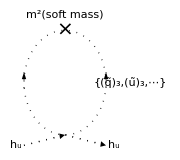
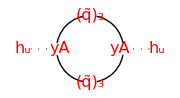
For E>>>m Suppose we add a squark mass this implies a log divergence.-Graphics-
Diagrams like these imply β-functions: UnderBar[∂]_t[m_(h_u^u)^2]→(y^2 (A^2+m_u_3^2+m_u_e^2+m_(q_3^3)^2))/(8 π)There are more complicated diagrams that contribute to running.-Graphics-
where the potential is V_soft→(ξ↔A y_t) h_u (q̃)_3 (ũ)_3+((ξ↔A y_t) h_u (q̃)_3 (ũ)_3)^† contributes the A^2 term in the β-function.
There also radiative corrections for external ũ and q̃ lines analogous to the h_u external lines.  The β functions become: UnderBar[∂]_t[m_(h_u^u)^2]→(y^2 factor[3] (A^2+m_u_3^2+m_u_e^2+m_(h_u^u)^2+m_(q_3^3)^2))/(8 π)UnderBar[∂]_t[m_((ũ)_3)^2]→(y^2 factor[2] (A^2+m_u_3^2+m_u_e^2+m_(h_u^u)^2+m_(q_3^3)^2))/(8 π)UnderBar[∂]_t[m_(q̃)^2]→(y^2 (A^2+m_u_3^2+m_u_e^2+m_(h_u^u)^2+m_(q_3^3)^2))/(8 π)
where the added factor[3] is due to 3 colors and factor[2] is due to SU[2] muliplets.  Color factors that go in and out are not part of the loop calculation.

```mathematica
PR1["For E>>>m ",
CG["Suppose we add a squark mass this implies a log divergence."],
Graphics[{Thick,Black,Dotted,
Circle[{0,0},1],
Line[{{-1,-1.2 },{ 0,-1}}],
Line[{{0,-1},{ 1,-1.2 }}],
Text[Style["m^2(soft mass)",TextAlignment->Left],{0,1.3}],
Text[Style["×",FontSize->20],{0,1}],
Arrowheads[{.1}],
Arrow[{{-1,-.1},{-1,.2}}],
Arrow[{{1,-.1},{1,.2}}],
Text[Style["{(q̃)_3,(ũ)_3,⋯}"],{1.6,0}],
Arrowheads[{.01,.1,.01}],Arrow[{{-1,-1.2 },{ 0,-1}}],
Text[Style["h_u"],{-1.2,-1.2}],
Arrowheads[{.01,.1}],Arrow[{{ 0,-1},{1,-1.2 }}],
Text[Style["h_u"],{1.2,-1.2}]
},ImageSize->Small
],

NL,"Diagrams like these imply β-functions: ",
xPartialD[Subscript[m, hd[u]]^2,t]->1/(8π)y^2(Subscript[m, qd[3]]^2+Subscript[m, Subscript[u, e]]^2+Subscript[m, Subscript[u, 3]]^2+A^2),
CG["There are more complicated diagrams that contribute to running."],
Graphics[{Thick,Black,
Circle[{0,0},1],
Dotted,Line[{{-2,0},{-1,0}}],
Line[{{2,0},{1,0}}],
TextOver["yA",{.9,-.0}],TextOver["yA",{-.9,-.0 }],
TextOver["h_u",{2,0 }],TextOver["h_u",{-2,0 }],
TextOver["(q̃)_3",{0,1 }],TextOver["(q̃)_3",{0,-1 }]
},ImageSize->Small
],
NL,"where the potential is ",
Subscript[V, soft]->(ξ↔A Subscript[y, t])Subscript[q̃, 3] Subscript[ũ, 3] Subscript[h, u]+SuperDagger[((ξ↔A Subscript[y, t])Subscript[q̃, 3] Subscript[ũ, 3] Subscript[h, u])],
" contributes the A^2 term in the β-function.
There also radiative corrections for external ũ and q̃ lines analogous to the h_u external lines.  The β functions become: ",
xPartialD[Subscript[m, hd[u]]^2,t]->factor[3]/(8π)y^2(Subscript[m, qd[3]]^2+Subscript[m, Subscript[u, e]]^2+Subscript[m, Subscript[u, 3]]^2+Subscript[m, hd[u]]^2+A^2),
xPartialD[Subscript[m, Subscript[ũ, 3]]^2,t]->factor[2]/(8π)y^2(Subscript[m, qd[3]]^2+Subscript[m, Subscript[u, e]]^2+Subscript[m, Subscript[u, 3]]^2+Subscript[m, hd[u]]^2+A^2),
xPartialD[Subscript[m, q̃]^2,t]->1/(8π)y^2(Subscript[m, qd[3]]^2+Subscript[m, Subscript[u, e]]^2+Subscript[m, Subscript[u, 3]]^2+Subscript[m, hd[u]]^2+A^2),
NL,"where the added factor[3] is due to 3 colors and factor[2] is due to SU[2] muliplets.  Color factors that go in and out are not part of the loop calculation.  "
];
```

```mathematica
PR1[CG["Radiative electro-weak symmetry breaking with only m_hd[u]^2<0 and q_t>>m ⟹ β-function forcing that is too strong.  We do know that y_t >> y_b where we have "],
NL,
W->Subscript[y, t][1].Subscript[Q, 3].Subscript[U, 3].Subscript[H, u][175]+Subscript[y, b][2].Subscript[Q, 3].Subscript[D, 3].Subscript[H, d]["?"]
]
```

Radiative electro-weak symmetry breaking with only m_hd[u]^2<0 and q_t>>m ⟹ β-function forcing that is too strong.  We do know that y_t >> y_b where we have 
W→y_b[2].Q_3.D_3.H_d[?]+y_t[1].Q_3.U_3.H_u[175]

```mathematica
PR1["Higgs potential ",
W->μ.Subscript[H, u].Subscript[H, d],
NL,
tmpV=V->(μ^2).(SuperDagger[hd[u]].hd[u]+SuperDagger[hd[d]].hd[d])+g^2/2(SuperDagger[hd[u]].τu[a].hd[u]+SuperDagger[hd[d]].τu[a].hd[d])^2+gp^2/2(SuperDagger[hd[u]].(1/2).hd[u]+SuperDagger[hd[d]].(-1/2).hd[d])^2+SoftOp[(Subscript[m, hu]^2).SuperDagger[hd[u]].hd[u]+(Subscript[m, hd]^2).SuperDagger[hd[d]].hd[d]]-Rephase[((Subscript[m, 3]^2).SuperDagger[hd[u]].hd[d]+SuperDagger[((Subscript[m, 3]^2).SuperDagger[hd[u]].hd[d])])],
NL,"We can rephase ",hd[u].hd[d]," such that ",Subscript[m, 3]^2∈ℝ,
NL,"As in the SM for VEV we assign a VEV structure for this case ",
subh={hd[u]->{{0},{v}},hd[d]->{{Subscript[v, 2]},{Subscript[v, 3]}}},
" where ",v∈ℝ,and,{Subscript[v, 2],Subscript[v, 3]}∈ℂ,
NL,"Plugging these into V",Yield,
"POFF",
tmp=tmpV/.subDaggerCT//simpleDot3[{μ,Subscript[m, 3]}]//ConjugateCTSimplify1[{Subscript[m, 3],v},{Subscript[m, _]^2}],Yield,
"PON",
tmpV1=tmp/.subh//ConjugateCTSimplify1[{Subscript[m, 3],v},{Subscript[m, _]^2}],Yield,
"Sum over τu[a]->σu[a]/2,{a,1,3}",Yield,
"POFF",
tmp=ExtractPositionPattern[tmpV1,Dot[a___,τu[a],b___]]/.τu[a]->σu[a]/2,Yield,
tmp=Map[ # [[1]]->Sum[#[[2]]/.sPauli,{a,{1,2,3}}]&,tmp],Yield,
"PON",
tmp=ReplacePart[tmpV1,tmp]//.List[a_]:>First[Flatten[a]],
NL,"Substitute: ",sub={Subscript[m, hu]^2->Subscript[m, 1]^2-μ^2,Subscript[m, hd]^2->Subscript[m, 2]^2-μ^2},Yield,
"POFF",
tmp=tmp/.sub//Simplify,Yield,
"PON",
tmpx=tmp=tmp/.Rephase[a_]->a/.SoftOp[a_]->a//Simplify,
CG["Assuming v_3->0 and V≠0 then charge symmetry is broken.  Investigate V at v_3->0.  With this change we change notation: "],
subn={Subscript[v, 3]->0,Subscript[v, 2]->v2,v->v1,Subscript[m, a_]->Subscript[μ, a]},Yield,
tmp=tmp/.subn//Simplify,Yield,
tmp=Collect[tmp,v3],Yield,
CR["The above relation for V is similar to the one shown in class except that it is missing a {-2 μ_3^2 v1 v2} term."]
]
```

Higgs potential W→μ.H_u.H_d
V→μ^2.((h_d^d)^†.h_d^d+(h_u^u)^†.h_u^u)+1/2 gp^2 ((h_d^d)^†.(-1/2).h_d^d+(h_u^u)^†.1/2.h_u^u)^2+1/2 g^2 ((h_d^d)^†.τ_a^a.h_d^d+(h_u^u)^†.τ_a^a.h_u^u)^2-Rephase[m_3^2.(h_u^u)^†.h_d^d+(m_3^2.(h_u^u)^†.h_d^d)^†]+SoftOp[m_hd^2.(h_d^d)^†.h_d^d+m_hu^2.(h_u^u)^†.h_u^u]
We can rephase h_u^u.h_d^d such that m_3^2∈ℝ
As in the SM for VEV we assign a VEV structure for this case {h_u^u→{{0},{v}},h_d^d→{{v_2},{v_3}}} where v∈ℝ and {v_2,v_3}∈ℂ
Plugging these into V
→ V→{{(gp^2 v^4)/8+v^2 μ^2+1/2 g^2 ({{0,v}}.τ_a^a.{{0},{v}})^2+g^2 {{0,v}}.τ_a^a.{{0},{v}} {{(v_2)^*,(v_3)^*}}.τ_a^a.{{v_2},{v_3}}+1/2 g^2 ({{(v_2)^*,(v_3)^*}}.τ_a^a.{{v_2},{v_3}})^2-Rephase[{{{{v (v_3)^* m_3^2+v m_3^2 v_3}}}}]+SoftOp[{{v^2 m_hu^2+m_hd^2 ((v_2)^* v_2+(v_3)^* v_3)}}]-1/4 gp^2 v^2 (v_2)^* v_2+μ^2 (v_2)^* v_2+1/8 gp^2 ((v_2)^*)^2 v_2^2-1/4 gp^2 v^2 (v_3)^* v_3+μ^2 (v_3)^* v_3+1/4 gp^2 (v_2)^* (v_3)^* v_2 v_3+1/8 gp^2 ((v_3)^*)^2 v_3^2}}
→ Sum over τu[a]->σu[a]/2,{a,1,3}
→ V→(g^2 v^4)/8+(gp^2 v^4)/8+v^2 μ^2-Rephase[v (v_3)^* m_3^2+v m_3^2 v_3]+SoftOp[v^2 m_hu^2+m_hd^2 ((v_2)^* v_2+(v_3)^* v_3)]-1/4 gp^2 v^2 (v_2)^* v_2+μ^2 (v_2)^* v_2+1/8 gp^2 ((v_2)^*)^2 v_2^2-1/4 gp^2 v^2 (v_3)^* v_3+μ^2 (v_3)^* v_3+1/4 gp^2 (v_2)^* (v_3)^* v_2 v_3+1/8 gp^2 ((v_3)^*)^2 v_3^2-1/2 g^2 v^2 (1/2 (v_2)^* v_2+(1/2+ⅈ/2) (v_3)^* v_2+(1/2-ⅈ/2) (v_2)^* v_3-1/2 (v_3)^* v_3)+1/2 g^2 (1/2 (v_2)^* v_2+(1/2+ⅈ/2) (v_3)^* v_2+(1/2-ⅈ/2) (v_2)^* v_3-1/2 (v_3)^* v_3)^2
Substitute: {m_hu^2→-μ^2+m_1^2,m_hd^2→-μ^2+m_2^2}
→ V→1/8 (g^2 v^4+gp^2 v^4+8 v^2 μ^2-2 gp^2 v^2 (v_2)^* v_2+8 μ^2 (v_2)^* v_2+gp^2 ((v_2)^*)^2 v_2^2-2 gp^2 v^2 (v_3)^* v_3+8 μ^2 (v_3)^* v_3+2 gp^2 (v_2)^* (v_3)^* v_2 v_3+gp^2 ((v_3)^*)^2 v_3^2-8 v m_3^2 ((v_3)^*+v_3)-2 g^2 v^2 ((v_3)^* ((1+ⅈ) v_2-v_3)+(v_2)^* (v_2+(1-ⅈ) v_3))+g^2 ((v_3)^* ((1+ⅈ) v_2-v_3)+(v_2)^* (v_2+(1-ⅈ) v_3))^2+8 (v^2 (-μ^2+m_1^2)+(-μ^2+m_2^2) ((v_2)^* v_2+(v_3)^* v_3)))Assuming v_3->0 and V≠0 then charge symmetry is broken.  Investigate V at v_3->0.  With this change we change notation: {v_3→0,v_2→v2,v→v1,m_a_→μ_a}
→ V→1/8 ((g^2+gp^2) v1^4+(g^2+gp^2) v2^2 (v2^*)^2+8 v1^2 μ_1^2-2 v2 v2^* ((g^2+gp^2) v1^2-4 μ_2^2))
→ V→1/8 ((g^2+gp^2) v1^4+(g^2+gp^2) v2^2 (v2^*)^2+8 v1^2 μ_1^2-2 v2 v2^* ((g^2+gp^2) v1^2-4 μ_2^2))
→ The above relation for V is similar to the one shown in class except that it is missing a {-2 μ_3^2 v1 v2} term.

```mathematica
PR1[CG["There is discussion of {μ_1,μ_2} parameter ranges for acceptable potential ranges.  The condition μ_1^2+μ_2^2 > 2 μ_3^2 is needed to prevent runaway V from below(?).  The condition  μ_1^2 μ_2^2 <  μ_3^4 is needed for electroweak symmetry breaking."]
]
```

There is discussion of {μ_1,μ_2} parameter ranges for acceptable potential ranges.  The condition μ_1^2+μ_2^2 > 2 μ_3^2 is needed to prevent runaway V from below(?).  The condition  μ_1^2 μ_2^2 <  μ_3^4 is needed for electroweak symmetry breaking.